## Utility codes: contains plot formatting and functions used latter

```mathematica
as = Directive[14,Black,FontFamily->"Arial"];
is = 300;
sf = {"Reverse",Identity};
ls =Directive[Black, FontFamily->"Arial",16];

aA = Style["A) \n", LineSpacing->{0.3, 0},as];
aB = Style["B) \n", LineSpacing->{0.3, 0},as];
aC = Style["C) \n", LineSpacing->{0.3, 0},as];
aD = Style["D) \n", LineSpacing->{0.3, 0},as];
aE = Style["E) \n", LineSpacing->{0.3, 0},as];
aF = Style["F) \n", LineSpacing->{0.3, 0},as];
aG = Style["G) \n", LineSpacing->{0.3, 0},as];
aH = Style["H) \n", LineSpacing->{0.3, 0},as];
aI = Style["I) \n", LineSpacing->{0.3, 0},as];
```

```mathematica
(* separate the type of abrupt changes
 and return pair of {time, 1} if increase and {time , -1} if decrease, make sure time goes from past to present (decreasing) 
*)
SeparateAC[data_,thresh_:0.5,Rand_:True]:= Module[{result,age,post,mean,pp,pos,AGE,PP},
age = data[[1]];
post = data[[2]];
mean = data[[3]];
Assert[Length@age ==Length@post == Length@mean];
pp =Unitize[post,thresh];
pos = Position[pp,1]//Flatten;
AGE= age[[pos]]+ If[Rand ==True, RandomReal[{-50,50.},Length@pos],0];

Quiet[
Do[
If[Mean[mean[[{i-1,i}]]] <Mean[ mean[[{i,i+1}]]], pp[[i]] = -1]; 
,{i,pos}];
];
PP = pp[[pos]];

result = Transpose[{AGE,PP}];
result
];

(* symbol used for figure 3*)
IT = Range[1000,11700,2000];
StyleSelector[age_]:= Which[
age ≤ IT[[2]],Graphics[{EdgeForm[{AbsoluteThickness[2], Black}],Black,Disk[{0,0},0.1]}],
IT[[2]]< age ≤ IT[[3]],Graphics[{EdgeForm[{AbsoluteThickness[2],GrayLevel[0.2]}],GrayLevel[0.2],Disk[{0,0},0.1]}],
IT[[3]]< age ≤ IT[[4]],Graphics[{EdgeForm[{AbsoluteThickness[2],GrayLevel[0.5]}],GrayLevel[0.5],Disk[{0,0},0.1]}],
IT[[4]]< age ≤ IT[[5]],Graphics[{EdgeForm[{AbsoluteThickness[2],GrayLevel[0.8]}],GrayLevel[0.8],Disk[{0,0},0.1]}],
IT[[5]]< age ,Graphics[{EdgeForm[{AbsoluteThickness[1],Gray}],White,Disk[{0,0},0.1]}]
 ];

st =Style[#,12,Black, FontFamily->"Arial"] &/@ { "11700",  "9000", "7000", "5000", "3000","1000"};

XY = Partition[Flatten[Table[{x,y},{x, Subdivide[39,48.,3]},{y,Subdivide[-88,-62.,7]}]],2];
```

## Lottery simulation codes

```mathematica
(* Simulates a lottery model assuming mortality of 3 species change throught time.
	T: duration of the simulation, f: dispersal (between 0 and 1), sT: standard deviation of total noise, sL: standard deviation of local noise, rho: strength of the spatial autocorrelation, SP is a matrix containing species parameters {beta, mu, s}, seed: random seed used for the runs *)

LotteryBoundary[T_,f_,sT_, sL_,rho_,SP_,seed_]:= Module[{ Fo,com,nsp,dist,FD,iocc,iocc1,occ,B0,B,MAT01, OCC0,OCC,bb,fbb,S,nocc,U,data,res,mat0,TS,TU,spl, defaultU,Ugrad,sG, Lx = 32+2, Ly = 16+2},

SeedRandom[seed];
(*COMMUNITY
	the first index (row) is for species Id
	the second index (column) is for mean birth, death, and sign and strength of density-dependence	 
*)
com = SP;
nsp = Length[SP]; (* total number of speices*)

(* initialize the occupancy, assume equal occupancy for all species*)
iocc1 = Table[0.02,{i,Lx},{j,Ly}];
iocc = Table[(1 - 0.02)/(nsp-1),{i,Lx},{j,Ly}];


occ = ConstantArray[iocc,nsp];
occ[[1]] = iocc1;

(* propagules productin *)
B0= Table[0.,{t,T},{i,Lx},{j,Ly}];
B = ConstantArray[B0,nsp];
MAT01 = Table[If[i == 1 ||j == 1 || i == Lx ||j == Ly, 0., 1.],{i,Lx},{j,Ly}]; (* takes 0 at the border, 1 otherwise *)

(* occupancy through time *)
OCC0=  Table[{},{t,T}];
OCC= ConstantArray[OCC0,nsp];

(* compute propagules production for each species through all time step.
rho is the correlation between regional stochasticity and local stochasticity,
1- rho = 0 ->  no regional stochasticity,
2- rho = 1 ->  stochasticty among all sites are prefectly correlated 
*)

If[rho ==0., 

Do[
B[[sp,t]] = MAT01 Exp[Log[com[[sp,1]] ] + RandomReal[NormalDistribution[0.,sL],{Lx,Ly}]];
,{t, T},{sp,nsp}],

sG = Sqrt[sT^2 - (1 -rho)^2 sL^2]/rho;

Do[
B[[sp,t]] = MAT01 Exp[Log[com[[sp,1]] ]+ rho RandomReal[NormalDistribution[0., sG]] + (1-rho) RandomReal[NormalDistribution[0.,sL],{Lx,Ly}]];
,{t, T},{sp,nsp}];
];

(* Creating a function that normalizes Fourier transform of the dispersal kernel *)
Fo[K_]:=Fourier[K]Sqrt[Lx Ly] /Total[Flatten[K]];

(*NSP is the first index, the second and third are for spatial coordinates*)
dist = Table[0.,{sp,nsp},{i,Lx},{j,Ly}];

(* Fourier transform of the dispersal kernel *)
FD = ConstantArray[{},nsp];
Do[
dist[[sp,{-1,2},{-1,1,2}]]=f/8;
dist[[sp,1,{-1,2}]] = f/8;
dist[[sp,1,1]] = (1-f);
FD[[sp]] =Fo[dist[[sp]]];
,{sp,nsp}];

bb = fbb = S =nocc=U= res= data =ConstantArray[{},nsp];
mat0 = Table[0,{i,Lx},{j,Ly}];

Do[ (* time *)

(* redistribution of seeds for lottery *)
TS =TU = mat0;
 Do[
bb[[sp]] = B[[sp,t]] occ[[sp]]; (* total propagules production per site *)
fbb[[sp]] = Fourier[bb[[sp]]];
S[[sp]] = InverseFourier[FD[[sp]]*fbb[[sp]]]//Re//Chop; (*redistributed propagules*)
TS+=S[[sp]]; (*total propagules*)

U[[sp]] = 1./(1. +(1.-com[[sp,2]] )/ com[[sp,2]] Exp[- com[[sp,3]] occ[[sp]]]);

TU+= U[[sp]]occ[[sp]]; (*total occupied site*)

,{sp,nsp}];

If[f == 0,TS += 1- MAT01]; (*this is ugly!!! the point is to avoid dividing by 0 below. It shouldn't matter for the edge as we anyway multiply by MAT01 *)

(* computes the next occupancy for each species *)
Do[
nocc[[sp]] = MAT01 (U[[sp]] occ[[sp]]+ (1. - TU) S[[sp]]/TS);
,{sp,nsp}];

(*stores data*)
Do[
occ[[sp]] = nocc[[sp]];
OCC[[sp,t]]=occ[[sp,2;;-2,2;;-2]];
,{sp,nsp}];

,{t,T}];
OCC
];
```

#### Code if same initial frequency

```mathematica
(* Simulates a lottery model assuming mortality of 2 species change throught time,  see below for the meaning of each variable but for MU1 (1 refers to the first species), the 3 entries are: 1- duration of the decline, 2- phase 1 mortality, 3- phase 2 mortality  *)

LotteryBoundarySameI[T_,f_,sT_, sL_,rho_,SP_,MU1_,seed_]:= Module[{ Fo,com,nsp,dist,FD,iocc,iocc1,occ,B0,B,MAT01, OCC0,OCC,bb,fbb,S,nocc,U,data,res,mat0,TS,TU,spl, defaultU,Ugrad, dt, ν0,ν1, Mu,sG, Lx = 32+2, Ly = 16+2},

(*If[f==0.,Print@"On works when dispersal (f) is strictly positive"; Abort[]];*)SeedRandom[seed];
(*COMMUNITY
	the first index (row) is for species Id
	the second index (column) is for mean birth, death, and sign and strength of density-dependence	 
*)
com = SP;
nsp = Length[SP]; (* total number of speices*)

(* Assumes a gradient in survival rate for the first species *)
dt = MU1[[1]];
ν0 = MU1[[2]];
ν1 = MU1[[3]];

(* USE IF MU for sp1 BECOMES TIME DEPENDENT 
Mu[t_]:= Module[{aa = (ν1 -ν0)/dt, cc,result,T2 = T/2},
cc= ν0 - aa T2;

result =
 If[t< T2, ν0,
 If[t> (T2+dt ),ν1,aa t +cc ]
];
result
];
*)

(* initialize the occupancy, assume equal occupancy for all species*)
(*iocc1 = Table[0.01,{i,Lx},{j,Ly}];*)
iocc = Table[1/nsp,{i,Lx},{j,Ly}];


occ = ConstantArray[iocc,nsp];
(*occ[[1]] = iocc1;
*)

(* propagules productin *)
B0= Table[0.,{t,T},{i,Lx},{j,Ly}];
B = ConstantArray[B0,nsp];
MAT01 = Table[If[i == 1 ||j == 1 || i == Lx ||j == Ly, 0., 1.],{i,Lx},{j,Ly}]; (* takes 0 at the border, 1 otherwise *)

(* occupancy through time *)
OCC0=  Table[{},{t,T}];
OCC= ConstantArray[OCC0,nsp];

(* compute propagules production for each species through all time step.
rho is the correlation between regional stochasticity and local stochasticity,
1- rho = 0 ->  no regional stochasticity,
2- rho = 1 ->  stochasticty among all sites are prefectly correlated 
*)

(*sG =If[rho ==0.,  10.^(-16), Sqrt[sT^2 - (1 -rho)^2 sL^2]/rho];*)

(*
Do[
B[[sp,t]] = MAT01 Exp[Log[com[[sp,1]] ]+ rho RandomReal[NormalDistribution[0, sG]] + (1-rho) RandomReal[NormalDistribution[0,sL],{Lx,Ly}]];
,{t, T},{sp,nsp}];*)

If[rho ==0., 

Do[
B[[sp,t]] = MAT01 Exp[Log[com[[sp,1]] ] + RandomReal[NormalDistribution[0.,sL],{Lx,Ly}]];
,{t, T},{sp,nsp}],

sG = Sqrt[sT^2 - (1 -rho)^2 sL^2]/rho;

Do[
B[[sp,t]] = MAT01 Exp[Log[com[[sp,1]] ]+ rho RandomReal[NormalDistribution[0., sG]] + (1-rho) RandomReal[NormalDistribution[0.,sL],{Lx,Ly}]];
,{t, T},{sp,nsp}];
];




(* Creating a function that normalizes Fourier transform of the dispersal kernel *)
Fo[K_]:=Fourier[K]Sqrt[Lx Ly] /Total[Flatten[K]];

(*NSP is the first index, the second and third are for spatial coordinates*)
dist = Table[0.,{sp,nsp},{i,Lx},{j,Ly}];

(* Fourier transform of the dispersal kernel *)
FD = ConstantArray[{},nsp];
Do[
dist[[sp,{-1,2},{-1,1,2}]]=f/8;
dist[[sp,1,{-1,2}]] = f/8;
dist[[sp,1,1]] = (1-f);
FD[[sp]] =Fo[dist[[sp]]];
,{sp,nsp}];

bb = fbb = S =nocc=U= res= data =ConstantArray[{},nsp];
mat0 = Table[0,{i,Lx},{j,Ly}];

Do[ (* time *)

(* redistribution of seeds for lottery *)
TS =TU = mat0;
 Do[
bb[[sp]] = B[[sp,t]] occ[[sp]]; (* total propagules production per site *)
fbb[[sp]] = Fourier[bb[[sp]]];
S[[sp]] = InverseFourier[FD[[sp]]*fbb[[sp]]]//Re//Chop; (*redistributed propagules*)
TS+=S[[sp]]; (*total propagules*)

U[[sp]] = 1./(1. +(1.-com[[sp,2]] )/ com[[sp,2]] Exp[- com[[sp,3]] occ[[sp]]]);

TU+= U[[sp]]occ[[sp]]; (*total occupied site*)

,{sp,nsp}];

If[f == 0,TS += 1- MAT01]; (*this is ugly!!! the point is to avoid dividing by 0 below. It shouldn't matter for the edge as we anyway multiply by MAT01 *)

(* computes the next occupancy for each species *)
Do[
nocc[[sp]] = MAT01 (U[[sp]] occ[[sp]]+ (1. - TU) S[[sp]]/TS);
,{sp,nsp}];

(*stores data*)
Do[
occ[[sp]] = nocc[[sp]];
OCC[[sp,t]]=occ[[sp,2;;-2,2;;-2]];
,{sp,nsp}];

,{t,T}];
OCC
];
```

# Final figures

## Empirical data formatting and exploration

```mathematica
ID = {238,494,503,516,532,795,871,971,973,986,1105,1136,1137,1615,1698,1820,1981,2023,2292,2332,3058,3131,3454,13047,14410,15032,(*15209,*)15350,15660,15682,15732,15764,15866,15892,15904,15909,15931,16189,16231,16271,17387,17404,18110,19842,20397,20512,20627};

(* 15209 is excluded because of a strange outlier *)
```

```mathematica
(* truncate the time-series to range between 11700-1000 BP, check that the ages are all different for each site *)
Do[
 dat = Import["/Users/gola/Box Sync/projects/paleo_lottery/hemlock_data/raw/raw_tsuga_"<>ToString@id<>".csv"][[2;;,2;;]];
If[DuplicateFreeQ[dat[[All,1]]]== False, Print[id]];
ndat = Select[dat, (#[[1]] ≤  11700 && #[[1]] ≥ 1000)& ];
ndat = Sort[ndat, (#1[[1]] ≥ #2[[1]])&];
Export["/Users/gola/Box Sync/projects/paleo_lottery/hemlock_data/tsuga_"<>ToString@id<>".csv",ndat];
,{id, ID}];
```

```mathematica
(* import fitted bcp *)
RD = PD = MD = {};
Do[
(* [[2;;-2]]: spans the data set from 2nd row to 2nd row from the last. This removes the header automatically generated from R and the last time series which cannot be fitted with bcp *)
 nd=Import["/Users/gola/Box Sync/projects/paleo_lottery/hemlock_data/tsuga_"<>ToString@id<>".csv"][[2;;-2]];
 pd=Import["/Users/gola/Box Sync/projects/paleo_lottery/hemlock_data/tsuga_pp_"<>ToString@id<>".csv"][[2;;-2]];
 md=Import["/Users/gola/Box Sync/projects/paleo_lottery/hemlock_data/tsuga_pm_"<>ToString@id<>".csv"][[2;;-2]];

Assert[Length@nd == Length@pd == Length@md];

AppendTo[RD,nd];
AppendTo[PD,pd];
AppendTo[MD,md];

,{id, ID}];
```

```mathematica
(* look manually here to select sites that contains at least an abrupt change *)
Manipulate[ListLinePlot[{RD[[i]],MD[[i]],PD[[i]]},PlotRange->{{1000,11700},{0,1}},GridLines->{None,{0.5}},ImageSize->500,Mesh->{{All,None,None}},AxesOrigin -> {11700,0} ,ScalingFunctions->sf,PlotLabel->ToString@ID[[i]]<>"_l_"<>ToString@Length[RD[[i]]]],{i,1,Length@ID,1}];
```

```mathematica
(* Site ID  for sites without and with abrupt changes *)
removeID = {494,503,795,1136,1137,1615,3131,3454,15032,15660,15764,15866,15892,15931,16189,16231,16271,20512,20627};
finalID = Complement[ID,removeID]
```

{238,516,532,871,971,973,986,1105,1698,1820,1981,2023,2292,2332,3058,13047,14410,15350,15682,15732,15904,15909,17387,17404,18110,19842,20397}

```mathematica
Length@finalID
```

27

## Figure 1

```mathematica
(* example of empirical data for figure 1A *)
e1 = Import["/Users/gola/Box Sync/projects/paleo_lottery/hemlock_data/tsuga_516.csv"][[2;;]];
e2 = Import["/Users/gola/Box Sync/projects/paleo_lottery/hemlock_data/tsuga_pm_516.csv"][[2;;]];
e3 = Import["/Users/gola/Box Sync/projects/paleo_lottery/hemlock_data/tsuga_pp_516.csv"][[2;;]];
```

```mathematica
SeparateAC[{e3[[All,1]],e3[[All,2]],e2[[2]]},0.5,False]
```

{{8324.5,1},{5600,1}}

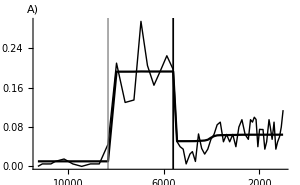

```mathematica
f1a =ListLinePlot[{e1,e2},
PlotRange-> {{1000,11500},{0,0.4}},AxesOrigin->{11500,0},
PlotStyle->{{Black,Thin},Black},AxesStyle->as,
GridLines->{{{5600,Directive[Black,AbsoluteThickness[1.25],Opacity[1]]},{8324.5,Directive[Gray,AbsoluteThickness[1.25],Opacity[0.75]]}}, None},
PlotRangePadding->None,ImageSize->is  ,ScalingFunctions->sf,
AxesLabel->aA
]
```

```mathematica
(* make sure the fitted bcp exist-need to run the R code first *)
e1 =Import["/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig2/sim_s_8_seed_5.csv"];
e2 = Import["/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig2/sim_pm_s_8_seed_5.csv"][[2;;,;;-2]];
e3 = Import["/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig2/sim_pp_s_8_seed_5.csv"][[2;;,;;-2]];

(* create age for the time-series *)
ne1 = {Range[11700,100,-200],e1[[10,;;;;2]]}//Transpose;
ne2 = {Range[11700,200,-200],e2[[10,;;;;2]]}//Transpose;
ne3 = {Range[11700,200,-200],e3[[10,;;;;2]]}//Transpose;
```

```mathematica
SeparateAC[{ne2[[All,1]],ne3[[All,2]],ne2[[All,2]]},0.5,True]
```

{{9082.52,-1},{6926.47,1},{725.468,-1},{486.25,-1}}

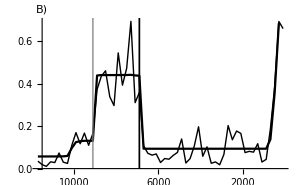

```mathematica
f1b =ListLinePlot[{ne1,ne2},
PlotRange-> {{1000,11500},{0,0.8}},AxesOrigin->{11500,0},
PlotStyle->{{Black,Thin},Black},AxesStyle->as,
GridLines->{{{9100,Directive[Gray,AbsoluteThickness[1.25],Opacity[0.75]]},{6900,Directive[Black,AbsoluteThickness[1.25],Opacity[1]]}}, None},
PlotRangePadding->None,ImageSize->is  ,ScalingFunctions->sf,
AxesLabel->aB
]
```

```mathematica
lg = PointLegend[{Gray,Black,Black,Gray},{"Original data","Fitted with bcp","Abrupt decrease","Abrupt increase"},LegendMarkers->{{Graphics[{Black,AbsoluteThickness[0.5],Line[{{1,0},{20,0}}]}],20},{"—",20},{"|",20},{"|",20}},LabelStyle->ls]
```

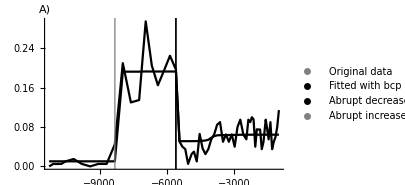
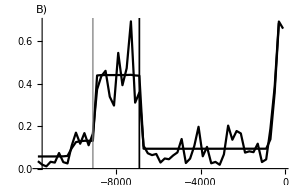
Real data | Simulated data
-Graphics- | -Graphics-Years Before PresentRelative abundance

```mathematica
F1 = Legended[Labeled[Grid[{{Style["Real data",FontFamily->"Arial",14],Style["Simulated data",FontFamily->"Arial",14]},{f1a,f1b }},Spacings->{{0,1},{0,0}}],{"Years Before Present","Relative abundance"},{Bottom,Left},RotateLabel->True,LabelStyle->ls],lg]
```

```mathematica
Export["/Users/gola/Box Sync/projects/paleo_lottery/latex/figs/fig1.pdf",F1]
```

/Users/gola/Box Sync/projects/paleo_lottery/latex/figs/fig1.pdf

## Figure 2

### Simulate as a function of s

```mathematica
Do[
 β = 20.; μ = 0.8; (* s =0.2;*)
SP  = {{β,μ,s},{β,μ,s},{β,μ,s}};

 TT = 1170;

out =LotteryBoundary[ TT,f =0.,σ= 0.8,Subscript[σ, l]=0.8, ρ =0.0, SP,seed = sed];

nout = out[[1,1;;-1;;10,1;;32;;4,1;;16;;4]];

dim = Dimensions[nout];
nout = Partition[Flatten[nout],dim[[2]]dim[[3]]]//Transpose;

SS =Round[s 20,1];(*Print@SS;*)

name = "/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig2/sim_s_"<>ToString[SS]<>"_seed_"<>ToString@sed<>".csv";
Export[ name,nout];
,{s,Range[0,0.5,0.05]},{sed,100}];
```

### Plot examples

```mathematica
SS = {0,5,8};
SITE = 14;

sed = 6;

d1 = Import["/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig2/sim_s_"<>ToString[SS[[1]]]<>"_seed_"<>ToString@sed<>".csv"][[SITE]];
d2 = Import["/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig2/sim_s_"<>ToString[SS[[2]]]<>"_seed_"<>ToString@sed<>".csv"][[SITE]];
d3= Import["/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig2/sim_s_"<>ToString[SS[[3]]]<>"_seed_"<>ToString@sed<>".csv"][[SITE]];

d1= {Range[11700,100,-100],d1}//Transpose;
d2= {Range[11700,100,-100],d2}//Transpose;
d3= {Range[11700,100,-100],d3}//Transpose;


d1m = Import["/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig2/sim_pm_s_"<>ToString[SS[[1]]]<>"_seed_"<>ToString@sed<>".csv"][[2;;,;;-2]][[SITE]];
d2m = Import["/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig2/sim_pm_s_"<>ToString[SS[[2]]]<>"_seed_"<>ToString@sed<>".csv"][[2;;,;;-2]][[SITE]];
d3m= Import["/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig2/sim_pm_s_"<>ToString[SS[[3]]]<>"_seed_"<>ToString@sed<>".csv"][[2;;,;;-2]][[SITE]];

d1m= {Range[11700,200,-100],d1m}//Transpose;
d2m= {Range[11700,200,-100],d2m}//Transpose;
d3m= {Range[11700,200,-100],d3m}//Transpose;

d1p = Import["/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig2/sim_pp_s_"<>ToString[SS[[1]]]<>"_seed_"<>ToString@sed<>".csv"][[2;;,;;-2]][[SITE]];
d2p = Import["/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig2/sim_pp_s_"<>ToString[SS[[2]]]<>"_seed_"<>ToString@sed<>".csv"][[2;;,;;-2]][[SITE]];
d3p= Import["/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig2/sim_pp_s_"<>ToString[SS[[3]]]<>"_seed_"<>ToString@sed<>".csv"][[2;;,;;-2]][[SITE]];

d1p= {Range[11700,200,-100],d1p}//Transpose;
d2p= {Range[11700,200,-100],d2p}//Transpose;
d3p= {Range[11700,200,-100],d3p}//Transpose;
```

```mathematica
Select[d1p,(#[[2]]>0.5)&]
```

{}

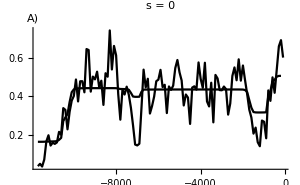
-Graphics-Years Before PresentSimulated frequency

```mathematica
f2a = Labeled[ListLinePlot[{d1,d1m},PlotRange->{{1000,11700},{0,1}},AxesOrigin->{11700,0},PlotStyle->{{Black,Thin},Black},PlotRangePadding->None,ImageSize->is,ScalingFunctions->sf ,
PlotLabel-> "s = 0" ,AxesLabel->aA,LabelStyle->ls,AxesStyle->as],{"Years Before Present", "Simulated frequency"},{Bottom,Left,Top},RotateLabel->True,LabelStyle->ls]
```

```mathematica
Select[d2p,(#[[2]]>0.5)&]
```

{}

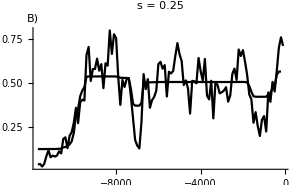
-Graphics-Years Before PresentSimulated frequency

```mathematica
f2b = Labeled[ListLinePlot[{d2,d2m},PlotRange->{{1000,11700},{0,1}},AxesOrigin->{11700,0},PlotStyle->{{Black,Thin},Black},AxesStyle->as,PlotRangePadding->None,ImageSize->is, ScalingFunctions->sf,PlotLabel-> "s = 0.25" ,LabelStyle->ls,
AxesLabel->aB
],{"Years Before Present", "Simulated frequency"},{Bottom,Left,Top},RotateLabel->True,LabelStyle->ls]
```

```mathematica
Select[d3p,(#[[2]]>0.5)&]
```

{{9500,0.9937},{7300,0.8708},{6100,0.9349},{1700,0.51}}

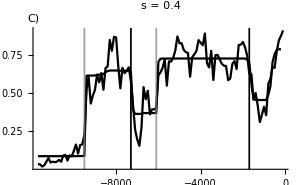
-Graphics-Years Before PresentSimulated frequency

```mathematica
f2c =Labeled[ ListLinePlot[{d3,d3m},PlotRange->{{1000,11700},{0,1}},AxesOrigin->{11700,0},PlotStyle->{{Black,Thin},Black},AxesStyle->as,PlotRangePadding->None,ImageSize->is ,ScalingFunctions->sf,
GridLines->{{{9500,Directive[Gray,AbsoluteThickness[1.25],Opacity[0.75]]},{7300,Directive[Black,AbsoluteThickness[1.25],Opacity[1]]},{6100,Directive[Gray,AbsoluteThickness[1.25],Opacity[0.75]]},{1700,Directive[Black,AbsoluteThickness[1.25],Opacity[1]]}}, None},PlotLabel-> "s = 0.4" ,LabelStyle->ls,AxesLabel->aC ],{"Years Before Present", "Simulated frequency"},{Bottom,Left,Top},RotateLabel->True,LabelStyle->ls]
```

### Plotting theoretical results

```mathematica
STT= SII = SDD = {};
Do[ (* for each seed *)
TT = II = DD = {};
Do[ (* for each value of s *)
dp = Import["/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig2/sim_pp_s_"<>ToString@s<>"_seed_"<>ToString@sed<>".csv"][[2;;,;;-2]];
dm = Import["/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig2/sim_pm_s_"<>ToString@s<>"_seed_"<>ToString@sed<>".csv"][[2;;,;;-2]];

lt = Length[dp[[1]]];
tt = Range[lt];
ll = Length[dp];
ACT = ACI  = ACD = {};
 Do[ (*for each site *)
tp = dp[[i]];
tm = dm[[i]];

ac = SeparateAC[{tt,tp,tm}][[All,2]];
act = Length[ac];
aci = Count[ac,-1];
acd = Count[ac,1];
AppendTo[ACT, act];
AppendTo[ACI, aci];
AppendTo[ACD, acd];
,{i,ll}];

AppendTo[TT, ACT];
AppendTo[II, ACI];
AppendTo[DD, ACD];
,{s,0,10,1}];

AppendTo[STT, TT];
AppendTo[SII,II];
AppendTo[SDD, DD];

,{sed,100}];
```

```mathematica
(* xx is for x coordinate for plotting *)
xx =Range[0,0.5,0.05];
mi = Table[SII[[rep,s]]//Mean//N,{s,Length@xx},{rep,100}];
md = Table[SDD[[rep,s]]//Mean//N,{s,Length@xx},{rep,100}];
msd = Table[STT[[rep,s]]//StandardDeviation//N,{s,Length@xx},{rep,100}];
```

```mathematica
(* for all abrupt increases *)
MI = {xx,Map[Mean,mi]}//Transpose;
(* if min-max envelop is needed;
MIAX ={xx,Map[Max,mi]}//Transpose;
MIIN ={xx,Map[Min,mi]}//Transpose;
*)
(* for all abrupt decreases *)
MD = {xx,Map[Mean,md]}//Transpose;
(* if min-ma envelop is needed;
MDAX ={xx,Map[Max,md]}//Transpose;
MDIN ={xx,Map[Min,md]}//Transpose;
*)
```

```mathematica
Map[Mean,mi]/Map[Mean,md]
```

{1.68307,1.6465,1.57272,1.51541,1.46214,1.47118,1.44353,1.45382,1.45013,1.40328,1.22591}

```mathematica
pr = {All,{0,3}};
ii = ListLinePlot[{MI},PlotRange->pr,PlotStyle->{Gray,LightRed,LightRed}(*,Filling->{2->{3}},FillingStyle->{LightRed,LightRed}*),PlotRangePadding->None];
dd = ListLinePlot[{MD},PlotRange->pr,PlotStyle->{Black,LightBlue,LightBlue}(*,Filling->{2->{3}},FillingStyle->{LightBlue,LightBlue}*),PlotRangePadding->None];
```

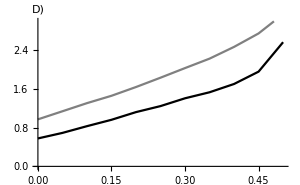
-Graphics-Strength of frequency-dependence (s)Average number of 
abrupt changes

```mathematica
f2d = Labeled[Show[ii,dd,(*ii2,dd2,*)LabelStyle->ls,ImageSize->is,AxesLabel->aD],{"Strength of frequency-dependence (s)", "Average number of \nabrupt changes"},{Bottom,Left},RotateLabel->True,LabelStyle->ls]
```

```mathematica
lg2 = LineLegend[{Black, Gray},{"Abrupt decreases", "Abrupt increases"}]
```

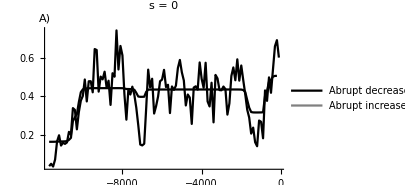
-Graphics-Years Before PresentSimulated frequency | -Graphics-Years Before PresentSimulated frequency
-Graphics-Years Before PresentSimulated frequency | -Graphics-Strength of frequency-dependence (s)Average number of 
abrupt changes

```mathematica
F2 = Legended[Grid[{{f2a, f2b}, {f2c,f2d}}],lg2]
```

```mathematica
Export["/Users/gola/Box Sync/projects/paleo_lottery/latex/figs/fig2.pdf",F2]
```

/Users/gola/Box Sync/projects/paleo_lottery/latex/figs/fig2.pdf

## Figure 3

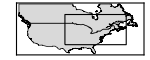

```mathematica
(*(* uncomment if an inset needs to be created *)f3inset =GeoGraphics[{{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],Black]],FaceForm[LightGray]],Polygon[ LinguisticAssistant]},{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],Black]],FaceForm[LightGray]],Polygon[ LinguisticAssistant]},EdgeForm[{Thick,Black}],FaceForm[],Rectangle[{-100,35},{-60,65}]}, GeoRange->{{25,60},{-130,-50}},ImageSize->150,Frame->True,FrameTicks->False,GeoBackground->GeoStyling[White], AspectRatio->1/2.5,GeoProjection->"Mercator"]
*)
```

```mathematica
(* get latitude and longitude coordinates*)
site = Import["/Users/gola/Box Sync/projects/paleo_lottery/hemlock_data/dataset_info.csv"][[2;;,{3,5,6}]];
 SAC  ={};
Do[(* for each site *)
id = finalID[[i]];
pos = Position[site[[All,1]],id][[1,1]];
coord = site[[pos,{2,3}]];
dm  =Import["/Users/gola/Box Sync/projects/paleo_lottery/hemlock_data/tsuga_pm_"<>ToString@id<>".csv"][[2;;-2]];
dp = Import["/Users/gola/Box Sync/projects/paleo_lottery/hemlock_data/tsuga_pp_"<>ToString@id<>".csv"][[2;;-2]];

temp = SeparateAC[{dp[[All,1]],dp[[All,2]],dm[[All,2]]},0.5, False];
ll = Length[temp];
sac = Partition[{temp,ConstantArray[coord, ll]}//Transpose//Flatten,4];

AppendTo[SAC,sac];
,{i,Length@finalID}];
```

```mathematica
(* separates the abrupt increase and decrease from the empirical data *)
DAT = Partition[SAC//Flatten,4];
empi = Select[DAT,(#[[2]]==-1 &)];
empd= Select[DAT,(#[[2]]==1 &)];
```

```mathematica
empi//Length
```

40

```mathematica
empd//Length
```

23

```mathematica
40/23.
```

1.73913

```mathematica
SeedRandom[1]; (* fix random seed so that the location of the dots are 'reproducible' *)
nD = Table[{GeoMarker[RandomReal[{-0.25,0.25},2] + empd[[i,{3,4}]],StyleSelector[empd[[i,1]]],"Scale"-> 1.0]},{i,Length@empd}];
nI = Table[{GeoMarker[RandomReal[{-0.25,0.25},2] + empi[[i,{3,4}]],StyleSelector[empi[[i,1]]],"Scale"-> 1.0]},{i,Length@empi}];
```

```mathematica
gr ={{37.,50.},{-90.,-60.}};
lg3 = BarLegend[GrayLevel,{0.2,0.5,0.9,0.91},"Ticks"-> {0, 0.3,0.4,0.8,1},"TickLabels" -> st,LegendMarkerSize->200,LegendLabel-> Style["YBP  ",16,FontFamily->"Arial"] ]
```

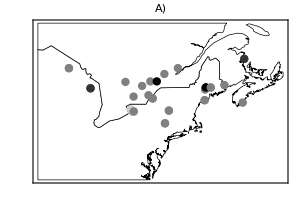

```mathematica
f3A=GeoGraphics[{{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],Black]],FaceForm[White]],Polygon[ LinguisticAssistant],nD},{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],Black]],FaceForm[White]],Polygon[ LinguisticAssistant],nD}},
GeoProjection-> "Mercator", GeoRange->gr,ImageSize->is,Frame->True,FrameTicks->False,GeoBackground->GeoStyling[White]
,PlotLabel->"A)                                                                     ",LabelStyle->Directive[Black,12,FontFamily->"Arial"] ]
```

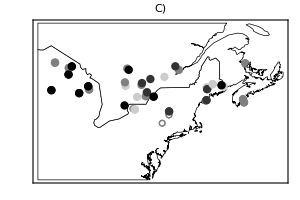

```mathematica
f3C=GeoGraphics[{{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],Black]],FaceForm[White]],Polygon[ LinguisticAssistant],nI},{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],Black]],FaceForm[White]],Polygon[ LinguisticAssistant],nI}}, 
GeoProjection-> "Mercator",GeoRange->gr,ImageSize->is,Frame->True,FrameTicks->False,GeoBackground->GeoStyling[White]
,PlotLabel->"C)                                                                     ",LabelStyle->Directive[Black,12,FontFamily->"Arial"]]
```

```mathematica
(* import an illustrative example*)

RR = 5; sed=1;
name = "/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig5a/sim_r_"<>ToString[RR]<>"_seed_"<>ToString@sed<>".csv";
dat = Import[name];

namep = "/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig5a/sim_pp_r_"<>ToString[RR]<>"_seed_"<>ToString@sed<>".csv";
namem = "/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig5a/sim_pm_r_"<>ToString[RR]<>"_seed_"<>ToString@sed<>".csv";
dp = Import[namep][[2;;,;;-2]];
dm = Import[namem][[2;;,;;-2]];
```

```mathematica
SAC1  ={};
RandomSeed[1];
XX = Range[11700,200,-100];
Do[(* for each site *)

coord = XY[[i]];
temp = SeparateAC[{XX+ RandomReal[{-50,50},Length@XX],dp[[i]],dm[[i]]},0.5, False];
ll = Length[temp];
sac = Partition[{temp,ConstantArray[coord, ll]}//Transpose//Flatten,4];

AppendTo[SAC1,sac];
,{i,32}];
```

```mathematica
(* separates the abrupt increase and decrease from the simulated data *)
DAT1 = Partition[SAC1//Flatten,4];
simd1 =Select[DAT1,#[[2]] == 1 &][[All,{1,3,4}]]//Sort;
simi1  = Select[DAT1,#[[2]] == -1 &][[All,{1,3,4}]]//Sort;
```

```mathematica
SeedRandom[1];
nD1 = Table[{GeoMarker[RandomReal[{-0.75,0.75},2] + simd1[[i,{2,3}]],StyleSelector[simd1[[i,1]]],"Scale"-> 1.0]},{i,Length@simd1}];
nI1 = Table[{GeoMarker[RandomReal[{-0.75,0.75},2] + simi1[[i,{2,3}]],StyleSelector[simi1[[i,1]]],"Scale"-> 1.0]},{i,Length@simi1}];
```

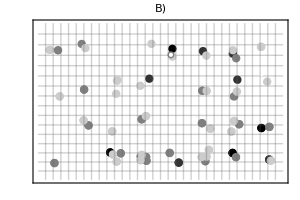

```mathematica
f3B=GeoGraphics[{{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],White]],FaceForm[White]],Polygon[ LinguisticAssistant],nD1},{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],White]],FaceForm[White]],Polygon[ LinguisticAssistant],nD1}},GeoGridLines->{Subdivide[37,50,16],Subdivide[-90.,-60.,32]},
GeoProjection-> "Mercator", GeoRange->gr,ImageSize->is,Frame->True,FrameTicks->False,GeoBackground->GeoStyling[White]
,PlotLabel->"B)                                                                     ",LabelStyle->Directive[Black,12,FontFamily->"Arial"]]
```

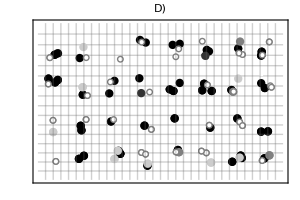

```mathematica
f3D=GeoGraphics[{{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],White]],FaceForm[White]],Polygon[ LinguisticAssistant],nI1},{GeoStyling[EdgeForm[Directive[AbsoluteThickness[0.5],White]],FaceForm[White]],Polygon[ LinguisticAssistant],nI1}},GeoGridLines->{Subdivide[37,50,16],Subdivide[-90.,-60.,32]},
GeoProjection-> "Mercator", GeoRange->gr,ImageSize->is,Frame->True,FrameTicks->False,GeoBackground->GeoStyling[White]
,PlotLabel->"D)                                                                     ",LabelStyle->Directive[Black,12,FontFamily->"Arial"]]
```

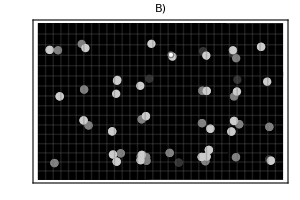
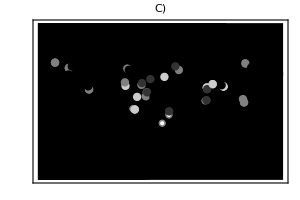
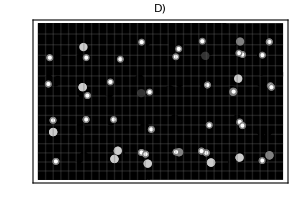
| Hemlock data | Simulated data
Abrupt decreases | -Graphics- | -Graphics-
Abrupt increases | -Graphics- | -Graphics-

```mathematica
F3 =  Legended[Grid[{{"",Style["Hemlock data",18, FontFamily->"Arial"], Style["Simulated data",18, FontFamily->"Arial"]},{Rotate[Style["Abrupt decreases",18, FontFamily->"Arial"],Pi/2],f3A,f3B},{Rotate[Style["Abrupt increases",18, FontFamily->"Arial"],Pi/2],f3C,f3D}}],lg3]
```

```mathematica
Export["/Users/gola/Box Sync/projects/paleo_lottery/latex/figs/fig3.pdf",F3]
```

/Users/gola/Box Sync/projects/paleo_lottery/latex/figs/fig3.pdf

## Figure 4

```mathematica
(* manually selected ticks for the y-axis*)
tx = {Automatic,{{0,"0.0"},{0.0005,"0.5"},{0.001,"1.0"}}};
```

```mathematica
(* import empirical data *)
DA = SAC  ={};
Do[ (* for each site *)

da = Import["/Users/gola/Box Sync/projects/paleo_lottery/hemlock_data/tsuga_"<>ToString@id<>".csv"][[2;;-2]];
dm  =Import["/Users/gola/Box Sync/projects/paleo_lottery/hemlock_data/tsuga_pm_"<>ToString@id<>".csv"][[2;;-2]];
dp = Import["/Users/gola/Box Sync/projects/paleo_lottery/hemlock_data/tsuga_pp_"<>ToString@id<>".csv"][[2;;-2]];

dp = {dp[[All,1]],Unitize[dp[[All,2]],0.5]}//Transpose;
sac = SeparateAC[{dp[[All,1]],dp[[All,2]],dm[[All,2]]},0.5, False];

AppendTo[DA,da];
AppendTo[SAC,sac];
,{id,finalID}];
```

```mathematica
pr3a = {{1200,10500},{0,0.6}};
pr3aa= {{1200,10500},{0,1.0}};
pr3b =  {{1200,10500},{0,0.001}};
```

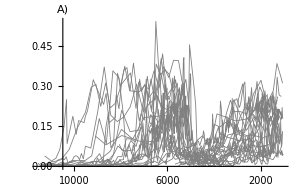

```mathematica
f4A=ListLinePlot[DA,PlotRange->pr3a,AxesOrigin->{10500,0},PlotStyle->Directive[Gray,AbsoluteThickness[0.6]],AxesStyle->as,PlotRangePadding->None,ImageSize->is ,ScalingFunctions->sf,LabelStyle->ls ,AxesLabel->aA]
```

```mathematica
(* separates the abrupt increase and decrease from the empirical data *)
dat =Partition[SAC//Flatten,2]//Sort;
empi = Select[dat,(#[[2]]==-1 &)][[All,1]];
empd = Select[dat,(#[[2]]==1 &)][[All,1]];

g1  = {empd,ConstantArray[Directive[Black,AbsoluteThickness[1],Opacity[1]],Length[empd]]}//Transpose;
g2  = {empi,ConstantArray[Directive[Gray,AbsoluteThickness[1],Opacity[1]],Length[empi]]}//Transpose;
```

```mathematica
(* compute the coefficient of variation *)
edi = Differences[empi] ;
edd = Differences[empd] ;
cvi1 = StandardDeviation@edi/Mean@edi; 
cvd1 = StandardDeviation@edd/Mean@edd;
```

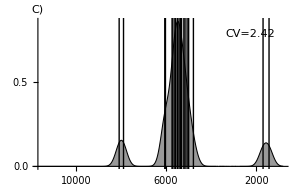

```mathematica
f4C= SmoothHistogram[empd,{200,"Gaussian"},
Epilog->Text[Framed[Style["CV="<>ToString@Round[cvd1,0.02],12,FontFamily->"Arial"],Background->White],Scaled[{0.85,.9}]],AxesStyle -> as,PlotStyle->Directive[AbsoluteThickness[0.75],Black],Filling->Bottom,FillingStyle->GrayLevel[0.6],PlotRange-> {{800,11700},{0,0.001}},AxesOrigin-> {11700,0},ScalingFunctions->sf,GridLines->{g1,None},LabelStyle->ls,AxesLabel->aC,ImageSize->is,Ticks->tx,PlotRangeClipping->False]
```

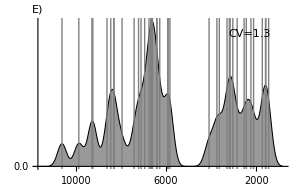

```mathematica
f4E = SmoothHistogram[empi,{200,"Gaussian"},
Epilog->Text[Framed[Style["CV="<>ToString@Round[cvi1,0.02],12,FontFamily->"Arial"],Background->White],Scaled[{0.85,.9}]],AxesStyle -> as,PlotStyle->Directive[AbsoluteThickness[0.75],Black],Filling->Bottom,FillingStyle->GrayLevel[0.6],PlotRange-> {{800,11700},{0,0.001}},AxesOrigin-> {11700,0},ScalingFunctions->sf,GridLines->{g2,None},LabelStyle->ls,AxesLabel->aE,ImageSize->is,Ticks->tx,PlotRangeClipping->False]
```

```mathematica
(* import a good looking simulated data, one needs to run codes for figure 5 first *)
RR =5; sed = 1;name = "/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig5a/sim_r_"<>ToString[RR]<>"_seed_"<>ToString@sed<>".csv";
dat2 = Import[name];

namep = "/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig5a/sim_pp_r_"<>ToString[RR]<>"_seed_"<>ToString@sed<>".csv";
namem = "/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig5a/sim_pm_r_"<>ToString[RR]<>"_seed_"<>ToString@sed<>".csv";
dp2 = Import[namep][[2;;,;;-2]];
dm2 = Import[namem][[2;;,;;-2]];
```

```mathematica
(* select some good looking sites *)
sID = {1,4,5,6,7,9,10,11,12,14,15,18,19,23,24,27,29,31,32};
simDA2 = Table[{Range[11700,100,-100] +RandomReal[{-50,50},117],dat2[[i]]}//Transpose,{i,sID}];
```

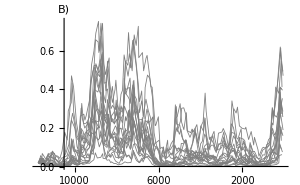

```mathematica
f4B= ListLinePlot[simDA2,PlotRange->pr3aa,AxesOrigin->{10500,0},PlotStyle->Directive[Gray,AbsoluteThickness[0.6]],AxesStyle->as,PlotRangePadding->None,ImageSize->is ,ScalingFunctions->sf,LabelStyle->ls ,AxesLabel->aB]
```

```mathematica
SeedRandom[1];
xx = Range[11700,100,-100];
SAC2= {};
Do[
 sac2 = SeparateAC[{xx + RandomReal[{-50,50},Length@xx],dp2[[i]],dm2[[i]]},0.5, False];
AppendTo[SAC2,sac2];

,{i, sID}];

(* separates the abrupt increase and decrease from the empirical data *)
sim2 =Partition[SAC2//Flatten,2]//Sort;
simi2 = Select[sim2,(#[[2]]==-1 &)][[All,1]];
simd2 = Select[sim2,(#[[2]]==1 &)][[All,1]];

g5  = {simd2,ConstantArray[Directive[Black,AbsoluteThickness[1],Opacity[1]],Length[simd2]]}//Transpose;
g6 = {simi2,ConstantArray[Directive[Gray,AbsoluteThickness[1],Opacity[1]],Length[simi2]]}//Transpose;
```

```mathematica
sdi2 = Differences[simi2] ;
sdd2 = Differences[simd2] ;
cvi3 = StandardDeviation@sdi2/Mean@sdi2; 
cvd3 = StandardDeviation@sdd2/Mean@sdd2;
```

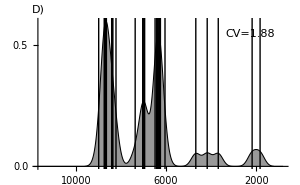

```mathematica
f4D= SmoothHistogram[simd2,{200,"Gaussian"},Epilog->Text[Framed[Style["CV="<>ToString@Round[cvd3,0.02],12,FontFamily->"Arial"],Background->White],Scaled[{0.85,.9}]],AxesStyle-> as, PlotStyle->Directive[AbsoluteThickness[0.75],Black],Filling->Bottom,FillingStyle->GrayLevel[0.6],PlotRange-> {{800,11700},{0,0.001}},AxesOrigin-> {11700,0},ScalingFunctions->sf,GridLines->{g5,None},LabelStyle->ls,ImageSize->is ,AxesLabel->aD,Ticks->tx]
```

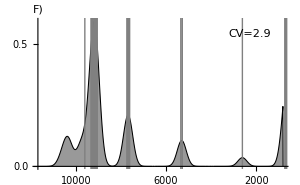

```mathematica
f4F= SmoothHistogram[simi2,{200,"Gaussian"},
Epilog->Text[Framed[Style["CV="<>ToString@Round[cvi3,0.02],12,FontFamily->"Arial"],Background->White],Scaled[{0.85,.9}]],AxesStyle-> as, PlotStyle->Directive[AbsoluteThickness[0.75],Black],Filling->Bottom,FillingStyle->GrayLevel[0.6],PlotRange-> {{800,11700},{0,0.001}},AxesOrigin-> {11700,0},ScalingFunctions->sf,GridLines->{g6,None},LabelStyle->ls, ImageSize->is ,AxesLabel->aF,Ticks->tx]
```

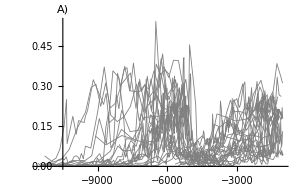
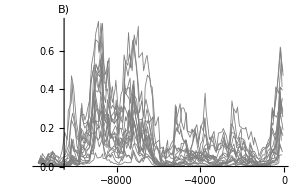
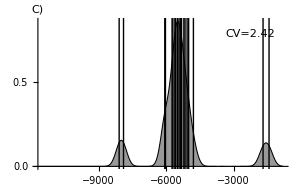
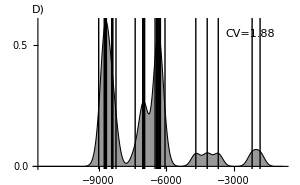
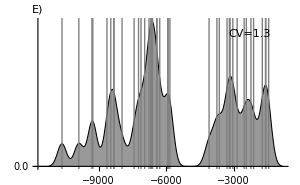
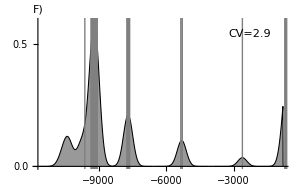
| Hemlock data | Simulated data (ρ = 0.5) | 
Relative abundance | -Graphics- | -Graphics- | 
Density | -Graphics- | -Graphics- | Abrupt decreases
Density | -Graphics- | -Graphics- | Abrupt increasesYears Before Present

```mathematica
F4 =Labeled[Grid[{{"",Style["Hemlock data",16,FontFamily->"Arial"],Style["Simulated data (ρ = 0.5)",16,FontFamily->"Arial"],""},{Rotate[Style["Relative abundance",16,FontFamily->"Arial"],Pi/2],f4A,f4B,""},{Rotate[Style["Density",16,FontFamily->"Arial"],Pi/2],f4C,f4D,Rotate[Style["Abrupt decreases",16,FontFamily->"Arial"],Pi/2]},{Rotate[Style["Density",16,FontFamily->"Arial"],Pi/2],f4E,f4F,Rotate[Style["Abrupt increases",16,FontFamily->"Arial"],Pi/2]}}],"Years Before Present",Bottom,LabelStyle->ls]
```

```mathematica
Export["/Users/gola/Box Sync/projects/paleo_lottery/latex/figs/fig4.pdf",F4]
```

/Users/gola/Box Sync/projects/paleo_lottery/latex/figs/fig4.pdf

#### recycle rho = 0, if one needs to show an intermediate scenario with the simulated data where rho = 0.

```mathematica
RR =0; sed = 1;name = "/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig5b/sim_r_"<>ToString[RR]<>"_seed_"<>ToString@sed<>"_s_0.2.csv";
dat1 = Import[name];

namep = "/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig5b/sim_pp_r_"<>ToString[RR]<>"_seed_"<>ToString@sed<>"_s_0.2.csv";
namem = "/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig5b/sim_pm_r_"<>ToString[RR]<>"_seed_"<>ToString@sed<>"_s_0.2.csv";
dp1 = Import[namep][[2;;,;;-2]];
dm1 = Import[namem][[2;;,;;-2]];
```

```mathematica
simDA1 = Table[{Range[11500,100,-100] +RandomReal[{-50,50},115],dat1[[i]]}//Transpose,{i,1,Length@dat1,2}];
```

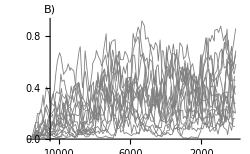

```mathematica
f4B= ListLinePlot[simDA1,PlotRange->pr3aa,AxesOrigin->{10500,0},PlotStyle->Directive[Gray,AbsoluteThickness[0.6]],AxesStyle->as,PlotRangePadding->None,ImageSize->is ,ScalingFunctions->sf,LabelStyle->ls ,AxesLabel->aB]
```

```mathematica
RandomSeed[1];
xx = Range[11500,200,-100];
SAC1= {};
Do[
 sac = SeparateAC[{xx + RandomReal[{-50,50},Length@xx],dp1[[i]],dm1[[i]]},0.5, False];
AppendTo[SAC1,sac];

,{i, 1,Length@dat,2}];

sim1 =Partition[SACx//Flatten,2]//Sort;
simi1 = Select[sim1,(#[[2]]==-1 &)][[All,1]];
simd1 = Select[sim1,(#[[2]]==1 &)][[All,1]];

g3  = {simd1,ConstantArray[Directive[Black,AbsoluteThickness[1],Opacity[1]],Length[simd1]]}//Transpose;
g4 = {simi1,ConstantArray[Directive[Gray,AbsoluteThickness[1],Opacity[1]],Length[simi1]]}//Transpose;
```

```mathematica
sdi1 = Differences[simi1] ;
sdd1 = Differences[simd1] ;
cvi2 = StandardDeviation@sdi1/Mean@sdi1; 
cvd2 = StandardDeviation@sdd1/Mean@sdd1;
```

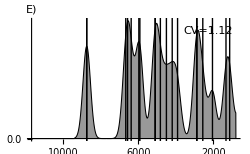

```mathematica
f4E= SmoothHistogram[simd1,{200,"Gaussian"},
Epilog->Text[Framed[Style["CV="<>ToString@Round[cvd2,0.02],12,FontFamily->"Arial"],Background->White],Scaled[{0.85,.9}]],AxesStyle-> as, PlotStyle->Directive[AbsoluteThickness[0.75],Black],Filling->Bottom,FillingStyle->GrayLevel[0.6],PlotRange-> {{800,11700},{0,0.001}},AxesOrigin-> {11700,0},ScalingFunctions->sf,GridLines->{g3,None},LabelStyle->ls,ImageSize->is ,AxesLabel->aE,Ticks->tx]
```

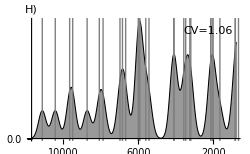

```mathematica
f4H= SmoothHistogram[simi1,{200,"Gaussian"},Epilog->Text[Framed[Style["CV="<>ToString@Round[cvi2,0.02],12,FontFamily->"Arial"],Background->White],Scaled[{0.85,.9}]],AxesStyle-> as, PlotStyle->Directive[AbsoluteThickness[0.75],Black],Filling->Bottom,FillingStyle->GrayLevel[0.6],PlotRange-> {{800,11700},{0,0.001}},AxesOrigin-> {11700,0},ScalingFunctions->sf,GridLines->{g4,None},LabelStyle->ls, ImageSize->is ,AxesLabel->aH,Ticks->tx]
```

```mathematica
F4 =Labeled[Grid[{{"",Style["Hemlock",16,FontFamily->"Arial"],Style["Simulated (ρ = 0.)",16,FontFamily->"Arial"],Style["Simulated (ρ = 0.5)",16,FontFamily->"Arial"],""},{Rotate[Style["Frequency",16,FontFamily->"Arial"],Pi/2],f4A,f4B,f4C,""},{Rotate[Style["Density",16,FontFamily->"Arial"],Pi/2],f4D,f4E,f4F,Rotate[Style["Abrupt decreases",16,FontFamily->"Arial"],Pi/2]},{Rotate[Style["Density",16,FontFamily->"Arial"],Pi/2],f4G,f4H,f4I,Rotate[Style["Abrupt increases",16,FontFamily->"Arial"],Pi/2]}}],"Years Before Present (YBP)",Bottom,LabelStyle->ls]
```

## Figure 5

### Change in spatial autocorrelation

```mathematica
Do[(* for each value of rho *)
 β = 20.; μ = 0.8;  s =0.3;
SP  = {{β,μ,s},{β,μ,s},{β,μ,s}};

 TT = 1170;

out =LotteryBoundary[ TT,ff  = 0.,σ= 0.7,Subscript[σ, l]=0.7, ρ =rr, SP,seed = SD];

(* selects time points every 10 decade and site every 4 cells *)
nout = out[[1,1;;-1;;10,1;;32;;4,1;;16;;4]];

dim = Dimensions[nout];
nout = Partition[Flatten[nout],dim[[2]]dim[[3]]]//Transpose;

RR =Round[rr 10,1];(*Print@RR;*)

name = "/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig5a/sim_r_"<>ToString[RR]<>"_seed_"<>ToString@SD<>".csv";
Export[ name,nout];
,{rr,Range[0,0.8,0.1]},{SD,1,100,1}];
```

```mathematica
TIME= Range[11700, 200, -100];
finalI = finalD = {};
Do[
ICV = DCV = {};
Do[

namep = "/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig5a/sim_pp_r_"<>ToString[i]<>"_seed_"<>ToString@sed<>".csv";
namem = "/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig5a/sim_pm_r_"<>ToString[i]<>"_seed_"<>ToString@sed<>".csv";
dp = Import[namep][[2;;,;;-2]];
dm = Import[namem][[2;;,;;-2]];

IAC= DAC = {};
Do[
rTIME= TIME + RandomReal[{-50,50},Length@TIME];
Assert[Length@rTIME == Length@dp[[j]]];
ac = SeparateAC[{rTIME,dp[[j]],dm[[j]]},0.5,False];
iac = Select[ac,(#[[2]] ==-1)&];
dac = Select[ac,(#[[2]] ==1)&];
AppendTo[IAC, iac];
AppendTo[DAC, dac];
,{j, Length@dp}];

IAC = Partition[IAC//Flatten,2][[All,1]]//Sort;
dI = Differences@IAC;

DAC = Partition[DAC//Flatten,2][[All,1]]//Sort;
dD = Differences@DAC;

(* compute CV*)
iCV = StandardDeviation@dI/ Mean@dI//N;
dCV = StandardDeviation@dD/ Mean@dD//N;

AppendTo[ICV , iCV];
AppendTo[DCV , dCV];
,{i,0,8,1}];
AppendTo[finalI, ICV];
AppendTo[finalD,DCV];

,{sed, 100}];
```

```mathematica
Mean@finalD
```

{1.0493,1.39767,1.73901,2.03841,2.41971,2.71868,3.06882,3.61853,1/100 (419.47+0.000261399 StandardDeviation[{3825.57}])}

```mathematica
419.47/99
```

4.23707

```mathematica
rg = Range[0,0.8,0.1];

mI ={rg,Mean@finalI}//Transpose;
(*
maxI = {rg,Map[Max,Transpose@finalI]}//Transpose;
minI = {rg,Map[Min,Transpose@finalI]}//Transpose;
*)

mD ={rg,Mean@finalD}//Transpose;

mD[[-1,-1]]=419.47/99; (* because in one replicate there was only one change so I removed that replicate, the CV is not defined*)

(*
maxD = {rg,Map[Max,Transpose@finalD]}//Transpose;
minD = {rg,Map[Min,Transpose@finalD]}//Transpose;
*)
```

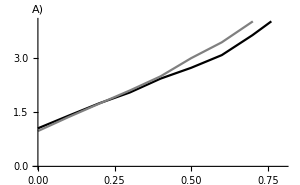
-Graphics-Coefficient of variationAutocorrelation (ρ)

```mathematica
f5a = Labeled[ListPlot[{mD, mI(*, maxD, minD,maxI,minI*)},PlotRange->{All,{0,4.}},Joined->True,PlotRangePadding->None,PlotStyle->{Black,Gray},AxesStyle->as,ImageSize-> is,AxesLabel->aA],{"Coefficient of variation","Autocorrelation (ρ)"},{Left, Bottom},RotateLabel->True,LabelStyle->ls]
```

### Change in dispersal

```mathematica
DAT = {};
Do[ (* for each value of f *)
 β = 20.; μ = 0.8;  s =0.3;
SP  = {{β,μ,s},{β,μ,s},{β,μ,s}};

 TT = 1170;

out =LotteryBoundary[ TT,ff ,σ= 0.8,Subscript[σ, l]=0.8, ρ =0., SP,seed = sed];

nout = out[[1,1;;-1;;10,1;;32;;4,1;;16;;4]];

dim = Dimensions[nout];
nout = Partition[Flatten[nout],dim[[2]]dim[[3]]]//Transpose;

FF =Round[ff 20,1];(*Print@FF;*)
(*AppendTo[DAT,nout];*)

name = "/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig5b/sim_f_"<>ToString[FF]<>"_seed_"<>ToString@sed<>".csv";
Export[ name,nout];
,{ff,Range[0.,0.5,0.05]},{sed,1,100,1}];
```

```mathematica
TIME= Range[11700, 200, -100];
finalI = finalD = {};
Do[
ICV = DCV = {};
Do[

namep = "/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig5b/sim_pp_f_"<>ToString[i]<>"_seed_"<>ToString@sed<>".csv";
namem = "/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/fig5b/sim_pm_f_"<>ToString[i]<>"_seed_"<>ToString@sed<>".csv";
dp = Import[namep][[2;;,;;-2]];
dm = Import[namem][[2;;,;;-2]];

IAC= DAC = {};
Do[
rTIME= TIME + RandomReal[{-50,50},Length@TIME];
Assert[Length@rTIME == Length@dp[[j]]];
ac = SeparateAC[{rTIME,dp[[j]],dm[[j]]},0.5,False];
iac = Select[ac,(#[[2]] ==-1)&];
dac = Select[ac,(#[[2]] ==1)&];
AppendTo[IAC, iac];
AppendTo[DAC, dac];
,{j, Length@dp}];

IAC = Partition[IAC//Flatten,2][[All,1]]//Sort;
dI = Differences@IAC;

DAC = Partition[DAC//Flatten,2][[All,1]]//Sort;
dD = Differences@DAC;

(* compute CV*)
iCV = StandardDeviation@dI/ Mean@dI//N;
dCV = StandardDeviation@dD/ Mean@dD//N;

AppendTo[ICV , iCV];
AppendTo[DCV , dCV];
,{i,0,10,1}];
AppendTo[finalI, ICV];
AppendTo[finalD,DCV];

,{sed, 100}];
```

```mathematica
mI ={Range[0,0.5,0.05],Mean@finalI}//Transpose;

(*maxI = {Range[0,0.5,0.05],Map[Max,Transpose@finalI]}//Transpose;
minI = {Range[0,0.5,0.05],Map[Min,Transpose@finalI]}//Transpose;*)

mD ={Range[0,0.5,0.05],Mean@finalD}//Transpose;
(*
maxD = {Range[0,0.5,0.05],Map[Max,Transpose@finalD]}//Transpose;
minD = {Range[0,0.5,0.05],Map[Min,Transpose@finalD]}//Transpose;
*)
```

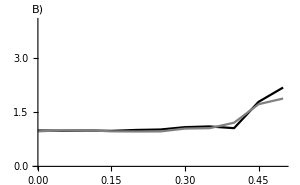
-Graphics-Coefficient of variationDispersal (f)

```mathematica
f5b = Labeled[ListPlot[{mD,mI(*, maxD, minD,maxI,minI*)},PlotRange->{All,{0,4}},Joined->True,LabelStyle->ls,PlotRangePadding->None,PlotStyle->{Black,Gray},AxesStyle->as,ImageSize-> is, AxesLabel->aB],{"Coefficient of variation","Dispersal (f)"},{Left, Bottom},RotateLabel->True,LabelStyle->ls]
```

```mathematica
lg5 = LineLegend[{Black, Gray},{"Abrupt decreases", "Abrupt increases"}]
```

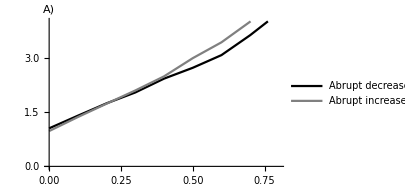
-Graphics-Coefficient of variationAutocorrelation (ρ) | -Graphics-Coefficient of variationDispersal (f)

```mathematica
F5 = Legended[Grid[{{f5a,f5b}},Spacings->{2, 1}],lg5]
```

```mathematica
Export["/Users/gola/Box Sync/projects/paleo_lottery/latex/figs/fig5.pdf",F5]
```

/Users/gola/Box Sync/projects/paleo_lottery/latex/figs/fig5.pdf

## Supplementary figures

### Figure S1

```mathematica
lgS = PointLegend[{Gray,Black,Gray},{"Original data","Fitted with bcp","Abrupt changes"},LegendMarkers->{{Graphics[{Black,AbsoluteThickness[0.5],Line[{{1,0},{20,0}}]}],20},{"—",20},{"|",20}},LabelStyle->ls]
```

```mathematica
(* import data for all empirical data (time-series, fitted mean, and posterior probability *)
ED = EP = EM ={};
Do[
ed = Import["/Users/gola/Box Sync/projects/paleo_lottery/hemlock_data/tsuga_"<>ToString@id<>".csv"][[2;;]];
em = Import["/Users/gola/Box Sync/projects/paleo_lottery/hemlock_data/tsuga_pm_"<>ToString@id<>".csv"][[2;;]];
ep = Import["/Users/gola/Box Sync/projects/paleo_lottery/hemlock_data/tsuga_pp_"<>ToString@id<>".csv"][[2;;]];

(*ep = {ep[[All,1]],Unitize[ep[[All,2]],0.6]}//Transpose;*)
ep = Select[ep,(#[[2]] > 0.5)&];
AppendTo[ED,ed];
AppendTo[EM,em];
AppendTo[EP,ep];
,{id,finalID}];
```

```mathematica
FIG = {};
Do[
gd = {Table[{EP[[i,j,1]],Directive[AbsoluteThickness[2],Opacity[1]]},{j,Length@EP[[i]]}],None};
fig = ListLinePlot[{ED[[i]],EM[[i]]},PlotRange->{All,{0,0.5}}, PlotStyle-> {{Black,Thin},Black},ScalingFunctions->{"Reverse",Identity},AxesOrigin->{Max[ED[[i,All,1]]],0},GridLines->gd,FrameStyle->Directive[12,Black,FontFamily->"Arial"],
PlotRangePadding->None,Frame->True,PlotLabel->"Dataset ID: "<>ToString@ID[[i]], LabelStyle->Directive[12,Black,FontFamily->"Arial"],ImageSize->250];
AppendTo[FIG,fig];
,{i,Length@EP}];
PrependTo[FIG,lgS];
```

```mathematica
FF = Partition[FIG,4];
out =Labeled[Grid[FF],{"Years Before Present","Frequency"},{Bottom,Left},RotateLabel->True,LabelStyle->Directive[16,Black,FontFamily->"Arial"]];
```

```mathematica
Export["/Users/gola/Box Sync/projects/paleo_lottery/latex/figs/figS1.pdf",out]
```

/Users/gola/Box Sync/projects/paleo_lottery/latex/figs/figS1.pdf

### Figure S2

```mathematica
(* runs a code assuming same initial conditions *)
STT= SII = SDD = {};
Do[
TT = II = DD = {};
Do[
dp = Import["/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/figS2_same_I/sim_pp_s_"<>ToString@s<>"_seed_"<>ToString@sed<>".csv"][[2;;,;;-2]];
dm = Import["/Users/gola/Box Sync/projects/paleo_lottery/simulated_data/figS2_same_I/sim_pm_s_"<>ToString@s<>"_seed_"<>ToString@sed<>".csv"][[2;;,;;-2]];

lt = Length[dp[[1]]];
tt = Range[lt];
ll = Length[dp];
ACT = ACI  = ACD = {};
 Do[
tp = dp[[i]];
tm = dm[[i]];

ac = SeparateAC[{tt,tp,tm}][[All,2]];
act = Length[ac];
aci = Count[ac,-1];
acd = Count[ac,1];
AppendTo[ACT, act];
AppendTo[ACI, aci];
AppendTo[ACD, acd];
,{i,ll}];

AppendTo[TT, ACT];
AppendTo[II, ACI];
AppendTo[DD, ACD];
,{s,0,16,1}];

AppendTo[STT, TT];
AppendTo[SII,II];
AppendTo[SDD, DD];

,{sed,10}];
```

```mathematica
xx =Range[0,0.5,0.05];
mi2 = Table[SII[[rep,s]]//Mean//N,{s,Length@xx},{rep,10}];
md2 = Table[SDD[[rep,s]]//Mean//N,{s,Length@xx},{rep,10}];
msd2 = Table[STT[[rep,s]]//StandardDeviation//N,{s,Length@xx},{rep,10}];
```

```mathematica
(* for abrupt increases *)
MI2 = {xx,Map[Mean,mi2]}//Transpose;
MIAX2 ={xx,Map[Max,mi2]}//Transpose;
MIIN2 ={xx,Map[Min,mi2]}//Transpose;

(* for all abrupt decreases *)
MD2 = {xx,Map[Mean,md2]}//Transpose;
MDAX2 ={xx,Map[Max,md2]}//Transpose;
MDIN2 ={xx,Map[Min,md2]}//Transpose;
```

```mathematica
ii2 = ListLinePlot[{MI2},PlotRange->pr,PlotStyle->Directive[Gray](*,Filling->{2->{3}},FillingStyle->{LightRed,LightRed}*),PlotRangePadding->None];
dd2= ListLinePlot[{MD2},PlotRange->pr,PlotStyle->Directive[Black](*,Filling->{2->{3}},FillingStyle->{LightBlue,LightBlue}*),PlotRangePadding->None];
```

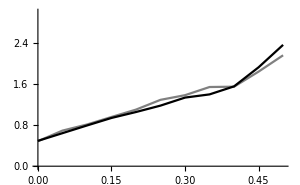
-Graphics-Strength of frequency dependence (s)Average number of 
abrupt changes

```mathematica
FS2 = Labeled[Show[ii2,dd2,LabelStyle->ls,ImageSize->is],{"Strength of frequency dependence (s)", "Average number of \nabrupt changes"},{Bottom,Left},RotateLabel->True,LabelStyle->ls]
```

```mathematica
Export["/Users/gola/Box Sync/projects/paleo_lottery/latex/figs/figS2.pdf",FS2]
```

/Users/gola/Box Sync/projects/paleo_lottery/latex/figs/figS2.pdf